```mathematica
gpu=Import[NotebookDirectory[]<>"4890.csv","CSV"];
cpu=Import[NotebookDirectory[]<>"Corei7.csv","CSV"];
quadcpu=Import[NotebookDirectory[]<>"Core2Quad.csv","CSV"];
oldcpu=Import[NotebookDirectory[]<>"E7200.csv","CSV"];
```

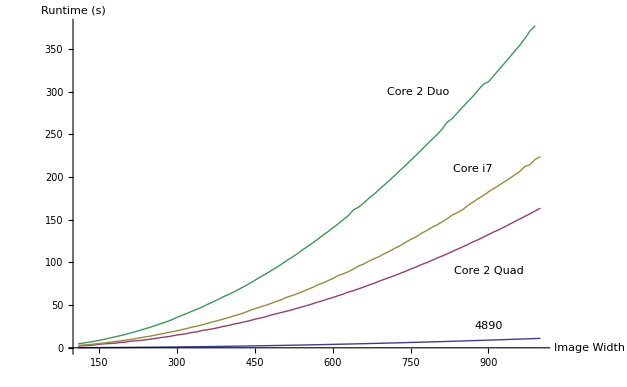

```mathematica
runtimePlot=Show[ListLinePlot[{gpu,quadcpu,cpu,oldcpu},PlotStyle->Thick,PlotRange->All,AxesOrigin->{100,0},AxesLabel->{"Image Width","Runtime (s)"}],Graphics[{
Text["Core 2 Quad",{900,90}],
Text["4890",{900,25}],
Text["Core 2 Duo",{765,300}],
Text["Core i7",{870,210}]
}]]
Export[NotebookDirectory[]<>"../paper/runtimePlot.pdf",runtimePlot];
```

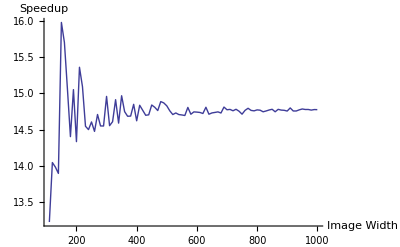

```mathematica
Speedup[a_,b_]:={a[[1]],b[[2]]/a[[2]]};
speedups=MapThread[Speedup,{gpu,quadcpu}];
speedupPlot=ListLinePlot[speedups,PlotStyle->Thick,PlotRange->All,AxesOrigin->{100,13},AxesLabel->{"Image Width","Speedup"}]
Export[NotebookDirectory[]<>"../paper/speedupPlot.pdf",speedupPlot];
```

```mathematica
strongScaling:=Import[NotebookDirectory[]<>"strong.csv","CSV"];
```

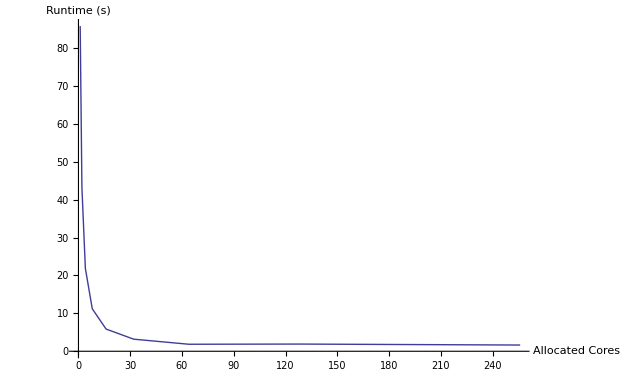

```mathematica
strongPlotOne=ListLinePlot[strongScaling,PlotStyle->Thick,AxesLabel->{"Allocated Cores","Runtime (s)"}]
Export[NotebookDirectory[]<>"../paper/strongPlotOne.pdf",strongPlotOne];
```

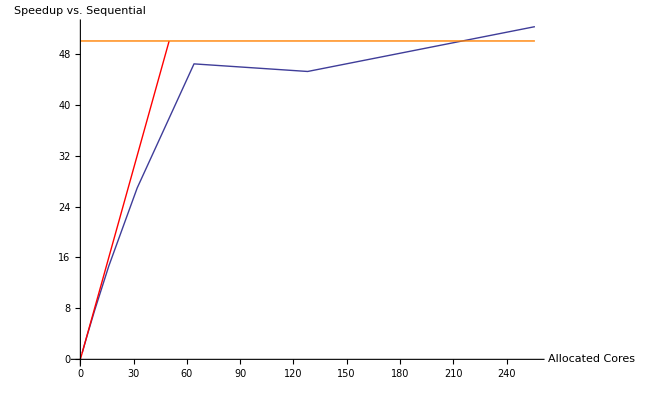

```mathematica
strongSpeedup={#[[1]],Last[First[strongScaling]]/#[[2]]}&/@strongScaling;
strongPlotTwo=Show[{ListLinePlot[strongSpeedup,PlotStyle->Thick,AxesLabel->{"Allocated Cores","Speedup vs. Sequential"}],Plot[x,{x,0,50},PlotStyle->{Red}],Plot[50,{x,0,256},PlotStyle->{Orange}]}]
Export[NotebookDirectory[]<>"../paper/strongPlotTwo.pdf",strongPlotTwo];
```

```mathematica
samples=500*500*2000;
gpuPerfPerDollar=samples/Last[gpu[[40]]]/250;
cpuPerfPerDollar=samples/Last[cpu[[40]]]/332;
quadcpuPerfPerDollar=samples/Last[quadcpu[[40]]]/851;
oldcpuPerfPerDollar=samples/Last[oldcpu[[40]]]/133;
dollarPlot=BarChart[{gpuPerfPerDollar,oldcpuPerfPerDollar,cpuPerfPerDollar,quadcpuPerfPerDollar},ChartLabels->Placed[{"4890","Core 2 Duo\nE7200","Core i7\n620M","Core 2 Quad\nQ6600"},Above],ChartStyle->"DarkRainbow",AxesLabel->"samp/s/$"]
Export[NotebookDirectory[]<>"../paper/dollarPlot.pdf",dollarPlot];
```

-Graphics-

```mathematica
gpuPerfPerDollar/oldcpuPerfPerDollar
```

18.6639

```mathematica
samples=500*500*2000;
gpuPerfPerTransistor=samples/Last[gpu[[40]]]/956;
cpuPerfPerTransistor=samples/Last[cpu[[40]]]/382;
quadcpuPerfPerTransistor=samples/Last[quadcpu[[40]]]/582;
oldcpuPerfPerTransistor=samples/Last[oldcpu[[40]]]/228;
transistorPlot=BarChart[{gpuPerfPerTransistor,oldcpuPerfPerTransistor,cpuPerfPerTransistor,quadcpuPerfPerTransistor},ChartLabels->Placed[{"4890","Core 2 Duo\nE7200","Core i7\n620M","Core 2 Quad\nQ6600"},Above],ChartStyle->"DarkRainbow",AxesLabel->"samp/s/\nM transistors"]
Export[NotebookDirectory[]<>"../paper/transistorPlot.pdf",transistorPlot];
```

-Graphics-

```mathematica
samples=500*500*2000;
gpuPerfPerWatt=samples/Last[gpu[[40]]]/285;
cpuPerfPerWatt=samples/Last[cpu[[40]]]/64.7;
quadcpuPerfPerWatt=samples/Last[quadcpu[[40]]]/90;
oldcpuPerfPerWatt=samples/Last[oldcpu[[40]]]/60;
wattPlot=BarChart[{gpuPerfPerWatt,oldcpuPerfPerWatt,cpuPerfPerWatt,quadcpuPerfPerWatt},ChartLabels->Placed[{"4890","Core 2 Duo\nE7200","Core i7\n620M","Core 2 Quad\nQ6600"},Above],ChartStyle->"DarkRainbow",AxesLabel->"samp/s/watt"]
Export[NotebookDirectory[]<>"../paper/wattPlot.pdf",wattPlot];
```

-Graphics-

```mathematica
gpuoverhead=Import[NotebookDirectory[]<>"4890-overhead.csv"];
cpuoverhead=Import[NotebookDirectory[]<>"Corei7-overhead.csv"];
```

```mathematica
gpuoverheadPercent={#[[1]],100*(#[[3]]/(#[[2]]+#[[3]]))}&/@gpuoverhead;
cpuoverheadPercent={#[[1]],100*(#[[3]]/(#[[2]]+#[[3]]))}&/@cpuoverhead;
```

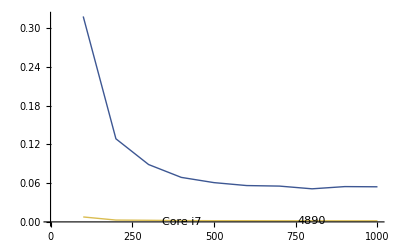

```mathematica
overheadPlot=Show[{ListLinePlot[{gpuoverheadPercent,cpuoverheadPercent},PlotStyle->{{Thick,RGBColor[.239,.341,.576]},{Thick,RGBColor[.855,.741,.318]}},AxesOrigin->{0,0},PlotRange->Full],
Graphics[{
Text["4890",{800,0.0007}],
Text["Core i7",{400,0.00015}]
}]}]
Export[NotebookDirectory[]<>"../paper/overheadPlot.pdf",overheadPlot];
```

```mathematica
gpuoverheadPercent
cpuoverheadPercent
```

{{100,0.318351},{200,0.128754},{300,0.0888634},{400,0.0689599},{500,0.0608517},{600,0.0563037},{700,0.0554817},{800,0.0512611},{900,0.0546973},{1000,0.054395}}

{{100,0.00766072},{200,0.00282974},{300,0.002484},{400,0.00202717},{500,0.00184247},{600,0.00184442},{700,0.00174547},{800,0.00173814},{900,0.00167174},{1000,0.00168572}}